# Euler 27

Euler discovered the remarkable quadratic formula:

n.b2 + n + 41

It turns out that the formula will produce 40 primes for the consecutive values n = 0 to 39. However, when n = 40, 402 + 40 + 41 = 40(40 + 1) + 41 is divisible by 41, and certainly when n = 41, 41.b2 + 41 + 41 is clearly divisible by 41.

The incredible formula  n.b2 − 79n + 1601 was discovered, which produces 80 primes for the consecutive values n = 0 to 79. The product of the coefficients, −79 and 1601, is −126479.

Considering quadratics of the form:

n.b2 + an + b, where |a| < 1000 and |b| < 1000

where |n| is the modulus/absolute value of n
e.g. |11| = 11 and |−4| = 4
Find the product of the coefficients, a and b, for the quadratic expression that produces the maximum number of primes for consecutive values of n, starting with n = 0.

## Nest

```mathematica
values={0};
n=0;
While[PrimeQ[Last[values]]||Last[values]==0,AppendTo[values,n^2+n+41];n++;]
n-1
```

40

```mathematica
nestBuilder[a_,b_]:=Module[
{
values={0},
n=0
},
While[PrimeQ[Last[values]]||Last[values]==0,AppendTo[values,n^2+a*n+b];n++;];
<|"Primes"->n-1,"a"->a,"b"->b|>
]
```

```mathematica
nestBuilder[-79,1601]
```

<|Primes→80,a→-79,b→1601|>

```mathematica
generateBs[a_]:=Table[nestBuilder[a,b],{b,-999,999}]
```

```mathematica
output=Table[nestBuilder[a,b],{a,-999,999},{b,-999,999}];
output=Flatten[output];
```

```mathematica
sel=output[[;;50]]
```

{<|Primes→0,a→-999,b→-999|>,<|Primes→0,a→-999,b→-998|>,<|Primes→1,a→-999,b→-997|>,<|Primes→0,a→-999,b→-996|>,<|Primes→0,a→-999,b→-995|>,<|Primes→0,a→-999,b→-994|>,<|Primes→0,a→-999,b→-993|>,<|Primes→0,a→-999,b→-992|>,<|Primes→1,a→-999,b→-991|>,<|Primes→0,a→-999,b→-990|>,<|Primes→0,a→-999,b→-989|>,<|Primes→0,a→-999,b→-988|>,<|Primes→0,a→-999,b→-987|>,<|Primes→0,a→-999,b→-986|>,<|Primes→0,a→-999,b→-985|>,<|Primes→0,a→-999,b→-984|>,<|Primes→1,a→-999,b→-983|>,<|Primes→0,a→-999,b→-982|>,<|Primes→0,a→-999,b→-981|>,<|Primes→0,a→-999,b→-980|>,<|Primes→0,a→-999,b→-979|>,<|Primes→0,a→-999,b→-978|>,<|Primes→1,a→-999,b→-977|>,<|Primes→0,a→-999,b→-976|>,<|Primes→0,a→-999,b→-975|>,<|Primes→0,a→-999,b→-974|>,<|Primes→0,a→-999,b→-973|>,<|Primes→0,a→-999,b→-972|>,<|Primes→1,a→-999,b→-971|>,<|Primes→0,a→-999,b→-970|>,<|Primes→0,a→-999,b→-969|>,<|Primes→0,a→-999,b→-968|>,<|Primes→1,a→-999,b→-967|>,<|Primes→0,a→-999,b→-966|>,<|Primes→0,a→-999,b→-965|>,<|Primes→0,a→-999,b→-964|>,<|Primes→0,a→-999,b→-963|>,<|Primes→0,a→-999,b→-962|>,<|Primes→0,a→-999,b→-961|>,<|Primes→0,a→-999,b→-960|>,<|Primes→0,a→-999,b→-959|>,<|Primes→0,a→-999,b→-958|>,<|Primes→0,a→-999,b→-957|>,<|Primes→0,a→-999,b→-956|>,<|Primes→0,a→-999,b→-955|>,<|Primes→0,a→-999,b→-954|>,<|Primes→2,a→-999,b→-953|>,<|Primes→0,a→-999,b→-952|>,<|Primes→0,a→-999,b→-951|>,<|Primes→0,a→-999,b→-950|>}

```mathematica
MaximalBy[output,Key["Primes"]]
```

{<|Primes→71,a→-61,b→971|>}

```mathematica
primes=output[[All,"Primes"]];
```

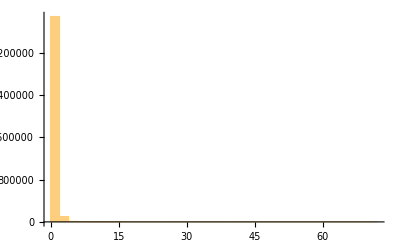

```mathematica
Histogram[primes]
```

```mathematica
Sort[primes][[-5;;]]
```

{67,68,69,70,71}

```mathematica
61*971
```

59231

```mathematica
Query[Select[(#a==-79&&#b==-999)&]]@output
```

{<|Primes→1,a→-79,b→-999|>}

```mathematica
%[[All,"Primes"]]
```

{1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1}

```mathematica
Max
```

```mathematica
MaximalBy
```

```mathematica
output[[2]]
```

{<|Primes→1,a→-998,b→-999|>,<|Primes→1,a→-998,b→-998|>,<|Primes→2,a→-998,b→-997|>,<|Primes→1,a→-998,b→-996|>,<|Primes→1,a→-998,b→-995|>,<|Primes→1,a→-998,b→-994|>,<|Primes→1,a→-998,b→-993|>,1986,<|Primes→1,a→-998,b→994|>,<|Primes→1,a→-998,b→995|>,<|Primes→1,a→-998,b→996|>,<|Primes→3,a→-998,b→997|>,<|Primes→1,a→-998,b→998|>,<|Primes→1,a→-998,b→999|>}
 |  |  |  |

```mathematica
generateBs[1]
```

{<|Primes→1,a→1,b→-999|>,<|Primes→1,a→1,b→-998|>,<|Primes→2,a→1,b→-997|>,<|Primes→1,a→1,b→-996|>,<|Primes→1,a→1,b→-995|>,<|Primes→1,a→1,b→-994|>,<|Primes→1,a→1,b→-993|>,1985,<|Primes→1,a→1,b→993|>,<|Primes→1,a→1,b→994|>,<|Primes→1,a→1,b→995|>,<|Primes→1,a→1,b→996|>,<|Primes→2,a→1,b→997|>,<|Primes→1,a→1,b→998|>,<|Primes→1,a→1,b→999|>}
 |  |  |  |

## Initial

```mathematica
Remove[formulaBuilde]
```

```mathematica
formulaBuilder[a_,b_]/;Abs[a]<1000&&Abs[b]<1000:=n^2+a*n+b
```

```mathematica
countPrimes[a_,b_]/;Abs[a]<1000&&Abs[b]<1000:=<|"Primes"->Length@Select[Table[n^2+a*n+b,{n,40}],PrimeQ],"a"->a,"b"->b|>
```

```mathematica
countPrimes[2,2]
```

<|Primes→18,a→2,b→2|>

```mathematica
generateBs[a_]:=Table[countPrimes[a,b],{b,-41,41}]
```

```mathematica
generateBs[1]
```

{<|Primes→9,a→1,b→-41|>,<|Primes→1,a→1,b→-40|>,<|Primes→20,a→1,b→-39|>,<|Primes→0,a→1,b→-38|>,<|Primes→25,a→1,b→-37|>,<|Primes→0,a→1,b→-36|>,<|Primes→22,a→1,b→-35|>,<|Primes→0,a→1,b→-34|>,<|Primes→19,a→1,b→-33|>,<|Primes→1,a→1,b→-32|>,<|Primes→47,a→1,b→-31|>,<|Primes→0,a→1,b→-30|>,<|Primes→44,a→1,b→-29|>,<|Primes→1,a→1,b→-28|>,<|Primes→15,a→1,b→-27|>,<|Primes→0,a→1,b→-26|>,<|Primes→37,a→1,b→-25|>,<|Primes→0,a→1,b→-24|>,<|Primes→29,a→1,b→-23|>,<|Primes→1,a→1,b→-22|>,<|Primes→13,a→1,b→-21|>,<|Primes→0,a→1,b→-20|>,<|Primes→44,a→1,b→-19|>,<|Primes→1,a→1,b→-18|>,<|Primes→26,a→1,b→-17|>,<|Primes→0,a→1,b→-16|>,<|Primes→17,a→1,b→-15|>,<|Primes→1,a→1,b→-14|>,<|Primes→43,a→1,b→-13|>,<|Primes→0,a→1,b→-12|>,<|Primes→32,a→1,b→-11|>,<|Primes→1,a→1,b→-10|>,<|Primes→22,a→1,b→-9|>,<|Primes→1,a→1,b→-8|>,<|Primes→31,a→1,b→-7|>,<|Primes→0,a→1,b→-6|>,<|Primes→27,a→1,b→-5|>,<|Primes→2,a→1,b→-4|>,<|Primes→24,a→1,b→-3|>,<|Primes→0,a→1,b→-2|>,<|Primes→49,a→1,b→-1|>,<|Primes→1,a→1,b→0|>,<|Primes→32,a→1,b→1|>,<|Primes→0,a→1,b→2|>,<|Primes→14,a→1,b→3|>,<|Primes→0,a→1,b→4|>,<|Primes→29,a→1,b→5|>,<|Primes→0,a→1,b→6|>,<|Primes→31,a→1,b→7|>,<|Primes→0,a→1,b→8|>,<|Primes→13,a→1,b→9|>,<|Primes→0,a→1,b→10|>,<|Primes→48,a→1,b→11|>,<|Primes→0,a→1,b→12|>,<|Primes→18,a→1,b→13|>,<|Primes→0,a→1,b→14|>,<|Primes→11,a→1,b→15|>,<|Primes→0,a→1,b→16|>,<|Primes→59,a→1,b→17|>,<|Primes→0,a→1,b→18|>,<|Primes→25,a→1,b→19|>,<|Primes→0,a→1,b→20|>,<|Primes→14,a→1,b→21|>,<|Primes→0,a→1,b→22|>,<|Primes→28,a→1,b→23|>,<|Primes→0,a→1,b→24|>,<|Primes→28,a→1,b→25|>,<|Primes→0,a→1,b→26|>,<|Primes→16,a→1,b→27|>,<|Primes→0,a→1,b→28|>,<|Primes→34,a→1,b→29|>,<|Primes→0,a→1,b→30|>,<|Primes→35,a→1,b→31|>,<|Primes→0,a→1,b→32|>,<|Primes→11,a→1,b→33|>,<|Primes→0,a→1,b→34|>,<|Primes→24,a→1,b→35|>,<|Primes→0,a→1,b→36|>,<|Primes→36,a→1,b→37|>,<|Primes→0,a→1,b→38|>,<|Primes→17,a→1,b→39|>,<|Primes→0,a→1,b→40|>,<|Primes→39,a→1,b→41|>}

```mathematica
createNumbers[a_]:=Table[formula[a,b,n],{b,-9,9},{n,1,5}]
```

```mathematica
createNumbers[2]
```

{{-6,-1,6,15,26},{-5,0,7,16,27},{-4,1,8,17,28},{-3,2,9,18,29},{-2,3,10,19,30},{-1,4,11,20,31},{0,5,12,21,32},{1,6,13,22,33},{2,7,14,23,34},{3,8,15,24,35},{4,9,16,25,36},{5,10,17,26,37},{6,11,18,27,38},{7,12,19,28,39},{8,13,20,29,40},{9,14,21,30,41},{10,15,22,31,42},{11,16,23,32,43},{12,17,24,33,44}}

```mathematica
Select[{{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12},{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33},{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44}},PrimeQ]
```

{}

```mathematica
countPrimes[a_]:=Table[<|"Primes"->Length@Select[formula[a,b,n],PrimeQ],"a"->a,"b"->b|>,{b,-9,9},{n,1,100}]
```

```mathematica
countPrimes[2]
```

Select::normal: Nonatomic expression expected at position 1 in Select[-6, PrimeQ].

Select::normal: Nonatomic expression expected at position 1 in Select[-1, PrimeQ].

Select::normal: Nonatomic expression expected at position 1 in Select[6, PrimeQ].

General::stop: Further output of Select :: normal will be suppressed during this calculation.

{{<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,89,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>,<|Primes→2,a→2,b→-9|>},17,{1}}
 |  |  |  |

```mathematica
Length@Select[Table[formula[a,b,n],{b,-9,9},{n,1,100}],PrimeQ]
```

0